## Prima di cominciare

Prima di cominciare sarà necessario clickare sul pulsante “Enable Dynamics” per permettere il corretto funzionamento della presentazione:

-Graphics-

Successivamente basterà premere “Start Presentation”:

-Graphics-

# Chips-Eaters Tutorial sul calcolo delle probabilità tramite mani di poker

## Gruppi Luca Raciti Gabriele Tamai Leonardo

## Introduzione

Questo template ha lo scopo di insegnare e introdurre l’utente al calcolo della porbabilità, sottoponendogli piccoli esercizi che crescono di difficoltà.
Abbiamo scelto 4 modalità :
La prima, molto semplice, consiste nel chiedere all’utente quanto è la probabilità di fare una coppia con solo l’estrazione di una carta.
La seconda e la terza chiedono all’utente di calcolare la probabilità di coppia o tris con tutte le carte coperte rimanenti sul banco.
La modalità 4 che introduce anche un numero randomico di avversari.

L’utente deve inserire il risultato sotto forma di frazione o formula,  l’esercizio restituisce giusto o sbagliato in base alla correttezza della risposta.
È stato implementato un bottone per la spiegazione dell’esercizio in cui in fondo è presente il risultato.
Sono presenti anche un bottone per generare un nuovo esercizio e una sezione per poter inserire il numero di un esercizio per poterlo rifare in futuro.

## Preparazione agli esercizi

Un mazzo di Poker è composto da 52 carte divise in 4 segni e per ogni segno ci sono 13 carte, dal valore 1 a K.

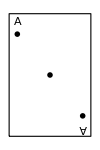
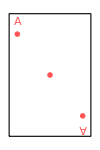
-Graphics- -Graphics- -Graphics- -Graphics-

```mathematica
Print[ResourceFunction["PlayingCardGraphic"][1,ImageSize->{100,150}]ResourceFunction["PlayingCardGraphic"][14,ImageSize->{100,150}]ResourceFunction["PlayingCardGraphic"][27,ImageSize->{100,150}]ResourceFunction["PlayingCardGraphic"][40,ImageSize->{100,150}]]
```

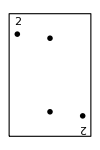
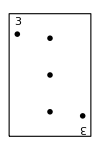
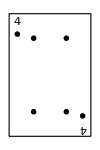
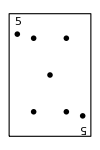
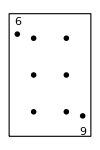
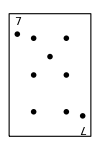
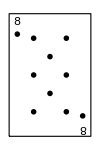
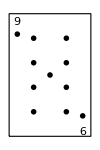
-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][1,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][2,ImageSize->{100,150}],"  ",
ResourceFunction["PlayingCardGraphic"][3,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][4,ImageSize->{100,150}],"  ",
ResourceFunction["PlayingCardGraphic"][5,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][6,ImageSize->{100,150}],"  ",
ResourceFunction["PlayingCardGraphic"][7,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][8,ImageSize->{100,150}],"  ",
ResourceFunction["PlayingCardGraphic"][9,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][10,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][11,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][12,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][13,ImageSize->{100,150}]}]]
```

## Calcolo probabilità: Coppia

## Probabilità di coppia

La prima modalità è quella di calcolare la probabilità di fare una coppia estraendo solo una carta.
Una coppia si forma quando tra le tue carte e quelle scoperte sul banco ci sono due carte con lo stesso numero e segno diverso.
come in questo caso:

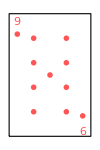
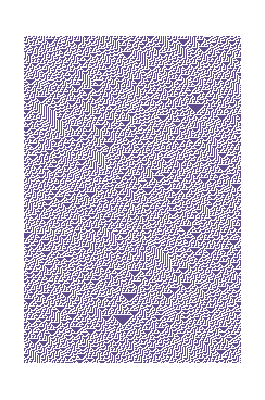
-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][10,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][22,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][39,ImageSize->{100,150}],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->{100,150}],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->{100,150}] }]]
```

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][8,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][48,ImageSize->{100,150}]}]]
```

-Graphics-  -Graphics-

Immaginiamo che ci siamo 3 carte scoperte sul banco e 2 sono quelle che abbiamo noi. Se l’esercizio ci chiede di calcolare la probabilità di coppia con una carte tra quelle che sono scoperte e quella carta non forma gia una coppia il calcolo della probabilità sarà quante carte ci sono ancora con il numero della carta scelta nel mazzo fratto tutte le carte ancora nel mazzo.

## Calcolo probabilità: Tris

La seconda modalità consiste nel calcolare la probabilità di fare un tris estraendo le due carte coperte rimanenti.
Un Tris si forma quando si hanno 3 carte dello stesso numero tra le carte sul banco e le carte nella mano del giocatore.
Per calcolare la probabilità prima è necessario controllare alcuni casi particolare, come nel caso in cui non ci sia alcuna coppia sul banco e ci sia solo
una carta coperta. In quel caso la probabilità è 0.
Oppure se gia è presenti un tris tra le certe del banco e quelle del giocatore.

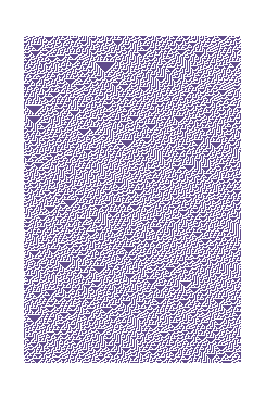
-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

-Graphics-  -Graphics-

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][10,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][22,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][39,ImageSize->{100,150}],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->{100,150}],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->{100,150}] }]]
```

bla bla bla

## Calcolo probabilità: Coppia estraendo le prossime due carte

La terza modalità consiste nel calcolare la probabilità di fare una coppia estraendo le prossime due carte.

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][10,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][22,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][39,ImageSize->{100,150}],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->{100,150}],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->{100,150}] }]]
```

-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][8,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][48,ImageSize->{100,150}]}]]
```

-Graphics-  -Graphics-

bla bla bla

## Calcolo probabilità: Coppia estraendo le prossime due carte, con avversari

La quarta modalità consiste nel calcolare la probabilità di fare una coppia estraendo le prossime due carte e considerando anche le carte degli avversari.
Carte degli avversari:

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][22,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][45,ImageSize->{100,150}]}]]
```

-Graphics-  -Graphics-

Carte del banco:

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][10,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][22,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][39,ImageSize->{100,150}],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->{100,150}],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->{100,150}] }]]
```

-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

La tua mano:

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][8,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][48,ImageSize->{100,150}]}]]
```

-Graphics-  -Graphics-

Bla bla bla

## Prova tu!

Premi il bottone sottostante per iniziare a provare tu stesso.
Verrà aperta una nuova finestra nella quale basterà andare nella sezione “Evaluation” e selezionare “Evaluate Notebook” come nell’immagine seguente:


-Graphics-

Buon divertimento!

```mathematica
SetDirectory[NotebookDirectory[]];
Print[Button["Gioca",NotebookOpen[NotebookDirectory[]<>"Main.nb"],
ImageSize->{200,100},
BaseStyle->{FontSize->46,FontFamily->"Impact", FontColor->Red}]]
```

Gioca